## Basic setup

The first 1000 primes with modulo 2^pedges can be assembled like so:

```mathematica
primesGraph[p_Integer:2, amount_Integer:1000]:=
Module[
{primes, accept,mapping,targets,adjMap},
primes = Array[Prime,amount];
accept = IntegerQ[Log[p,Abs[#1-#2]]]&;
mapping=Function[{u},Select[primes,accept[u,#]&]];
targets = mapping/@primes;
adjMap = Flatten[Apply[Function[{u},#1->u]/@#2&,Transpose[{primes,targets}],1]];
UndirectedGraph[adjMap] (*returns an undirected graph*)
]
```

The standard base-2 graph looks like the following:

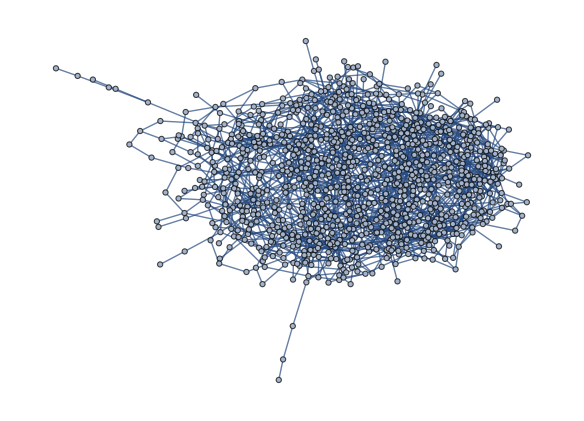

```mathematica
g2 = primesGraph[]
```

```mathematica
(*Export["/Users/swa/Desktop/primes-graph/g-2-1000.graphml",g];*)
```

The base-n graphs for n=2,..,100

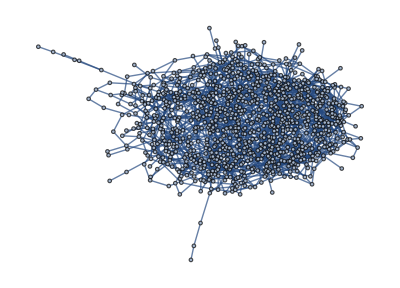
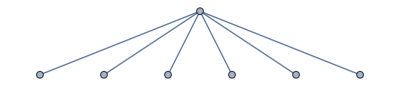
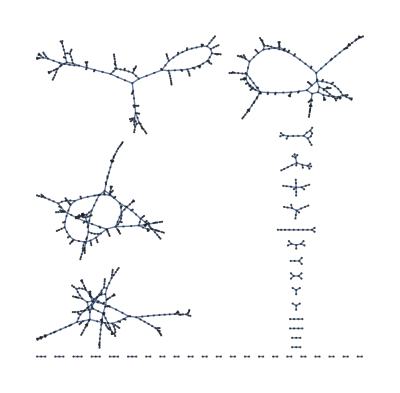

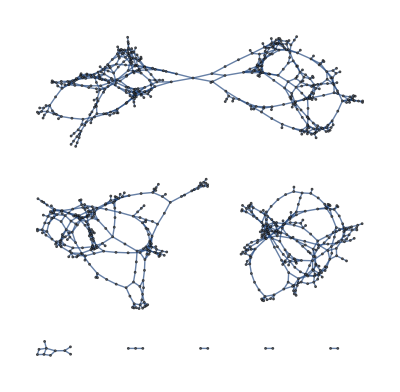

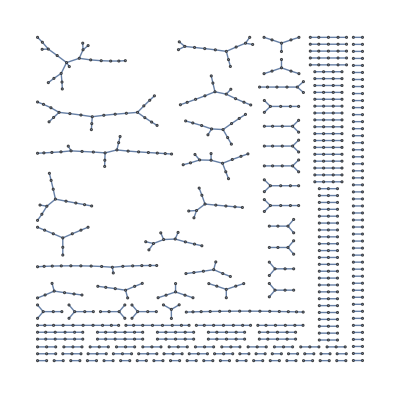

```mathematica
ga = Table[primesGraph[n],{n,2,100}];
ga[[1;;7]]
```

It seems the odd values gives a connected graph except for N=2:

```mathematica
ConnectedGraphQ/@ga
```

{True,True,False,True,False,True,False,True,False}

The diameter is obviously ∞ for odd values:

```mathematica
GraphDiameter/@ga
```

{14,2,∞,2,∞,1,∞,2,∞,2,∞,1,∞,2,∞,2,∞,1,∞,2,∞,1,∞,1,∞,2,∞,2,∞,1,∞,2,∞,2,∞,1,∞,2,∞,2,∞,1,∞,2,∞,1,∞,1,∞,2,∞,1,∞,1,∞,2,∞,2,∞,1,∞,1,∞,2,∞,1,∞,2,∞,2,∞,1,∞,1,∞,2,∞,1,∞,2,∞,1,∞,1,∞,2,∞,1,∞,1,∞,1,∞,2,∞,1,∞,2,∞}

If we take the odd ones only and skip the N=2 exception:

```mathematica
diameterSeries = Select[Drop[%33,1],NumberQ]
```

{2,2,1,2,2,1,2,2,1,2,1,1,2,2,1,2,2,1,2,2,1,2,1,1,2,1,1,2,2,1,1,2,1,2,2,1,1,2,1,2,1,1,2,1,1,1,2,1,2}

Let’s create an association for this:

```mathematica
trainN = Drop[Select[Range[100],OddQ],1];
diameterAssociations=  #[[1]]->#[[2]]&/@Transpose[{trainN,Select[Drop[%33,1],NumberQ]}]
```

{3→2,5→2,7→1,9→2,11→2,13→1,15→2,17→2,19→1,21→2,23→1,25→1,27→2,29→2,31→1,33→2,35→2,37→1,39→2,41→2,43→1,45→2,47→1,49→1,51→2,53→1,55→1,57→2,59→2,61→1,63→1,65→2,67→1,69→2,71→2,73→1,75→1,77→2,79→1,81→2,83→1,85→1,87→2,89→1,91→1,93→1,95→2,97→1,99→2}

Can something be learned here?

```mathematica
pr=Classify[diameterAssociations]
```

ClassifierFunction[…]

Let’s create a test set:

```mathematica
testN = Select[Range[101,150],OddQ];
testGraphs = primesGraph /@ testN;
diameterTestSeries = GraphDiameter/@ testGraphs;
diameterTestAssociations =#[[1]]->#[[2]]&/@Transpose[{testN,diameterTestSeries}]
```

{101→2,103→1,105→2,107→2,109→1,111→2,113→1,115→1,117→1,119→1,121→1,123→1,125→2,127→1,129→2,131→1,133→1,135→2,137→2,139→1,141→1,143→1,145→1,147→2,149→2}

```mathematica
pr[testN]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

That’s not encouraging. The classifier actually is a simple block function as can be seen from

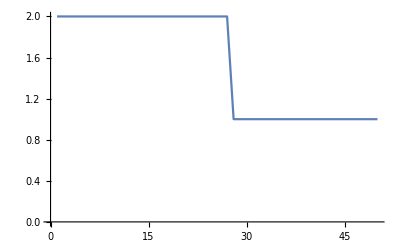

```mathematica
pr[Select[Range[1,100],OddQ]]//ListLinePlot
```

How does it look visually?

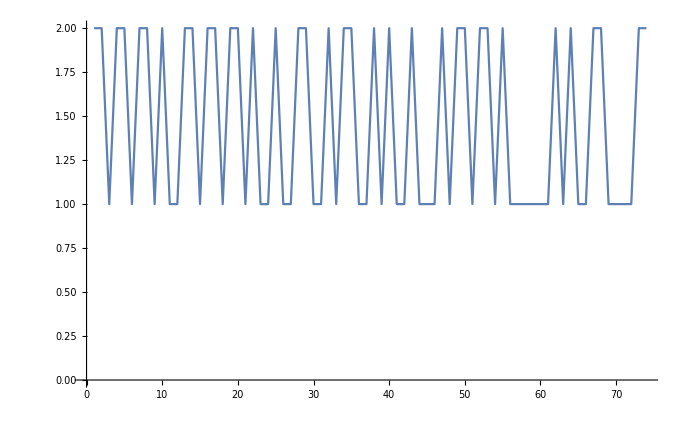

```mathematica
ListLinePlot[Flatten[{diameterSeries,diameterTestSeries}]]
```

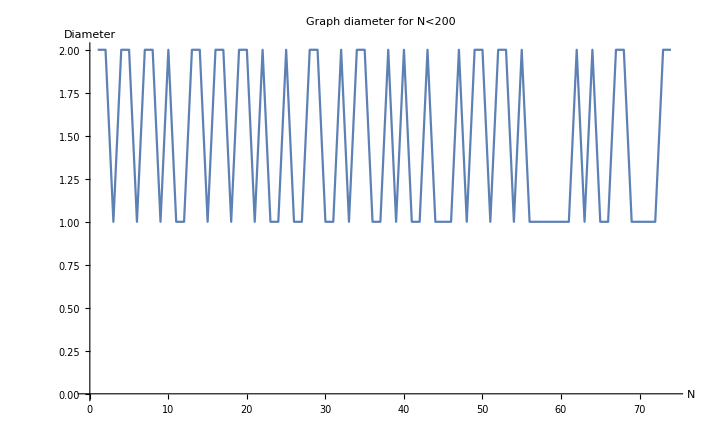

```mathematica
Show[%83,AxesLabel->{HoldForm[N],HoldForm[Diameter]},PlotLabel->HoldForm[Graph diameter for N<200],LabelStyle->{GrayLevel[0]}]
```

## Prime base

What about using prime bases? The first 100 primes:

```mathematica
gp = primesGraph/@ Array[Prime,100];
```

Here again, only N=2 stands out:

```mathematica
VertexCount/@gp
```

{995,7,4,2,3,2,3,2,2,3,2,2,3,2,2,2,3,2,2,3,2,2,2,2,2,3,2,3,2,2,2,2,3,2,3,2,2,2,2,2,3,2,3,2,3,2,2,2,3,2,2,3,2,2,2,2,3,2,2,3,2,2,2,3,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,2,2,2,2,3,2,2,2,2,2,2,2,2,3,2,2}

More visually:

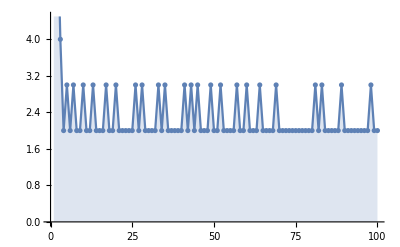

```mathematica
ListPlot[%18,Filling->Axis,Mesh->All,Joined->True]
```

This is equivalent to looking at the graph diameter:

```mathematica
GraphDiameter/@gp
```

{14,2,2,1,2,1,2,1,1,2,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,2,1,2,1,2,1,1,1,2,1,1,2,1,1,1,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1}

Since it looks so binary, let’s omit the first anomaly and see what number this produces:

```mathematica
Drop[%20/.{2->1,1->0},1]
```

{1,1,0,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
FromDigits[%28,2]
```

526290163330632824093045032964